```mathematica
f[n_]:=1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10
```

```mathematica
v=VandermondeMatrix[{x1,x2,x3,x4}]
```

VandermondeMatrix[…]

```mathematica
MatrixForm[v]
```

(1 | x1 | x1^2 | x1^3
1 | x2 | x2^2 | x2^3
1 | x3 | x3^2 | x3^3
1 | x4 | x4^2 | x4^3)

```mathematica
Det[v]
```

(-x1+x2) (-x1+x3) (-x2+x3) (-x1+x4) (-x2+x4) (-x3+x4)

```mathematica
N@Sin[Range[4]]
```

{0.841471,0.909297,0.14112,-0.756802}

```mathematica
v=VandermondeMatrix[N@Sin[Range[4]]]
```

VandermondeMatrix[…]

```mathematica
Normal[v]
```

{{1.,0.841471,0.708073,0.595823},{1.,0.909297,0.826822,0.751827},{1.,0.14112,0.0199149,0.00281038},{1.,-0.756802,0.57275,-0.433459}}

```mathematica
a=LinearSolve[v,N@Sin[Range[4]]]
```

{0.,1.,0.,0.}

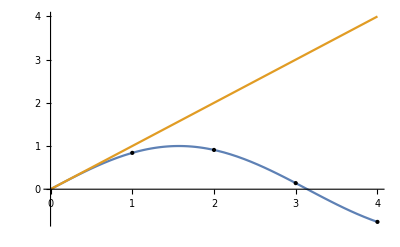

```mathematica
Plot[{Sin[x],a.{1,x,x^2,x^3}},{x,0,4},Epilog->Point@({Range[4],Sin[Range[4]]}ᵀ)]
```

```mathematica
xValues={0.5,1.,2.,4.}
```

{0.5,1.,2.,4.}

```mathematica
v=VandermondeMatrix[xValues]
```

VandermondeMatrix[…]

```mathematica
Normal[v]
```

{{1.,0.5,0.25,0.125},{1.,1.,1.,1.},{1.,2.,4.,8.},{1.,4.,16.,64.}}

```mathematica
a=LinearSolve[v,Cos[xValues]]
```

{0.987426,0.0744875,-0.655085,0.133474}

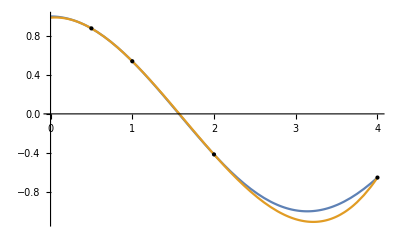

```mathematica
Plot[{Cos[x],a.{1,x,x^2,x^3}},{x,0,4},Epilog->Point@({{0.5,1.,2.,4.},Cos[{0.5,1.,2.,4.}]}ᵀ)]
```

```mathematica
f[x]
```

1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10

```mathematica
{xValues,fValues}=Transpose@Table[{x,f[x]},{x,Range[1]}]
```

{{1},{1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10}}

```mathematica
Vm=VandermondeMatrix[xValues]
```

VandermondeMatrix[…]

```mathematica
coefficients=LinearSolve[Vm,fValues]
```

{1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10}

```mathematica
poly[x_]=coefficients.x^(Range[Length[coefficients]]-1)
```

1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10

```mathematica
f[#]&/@ConstantArray[1,10]
```

{1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10}

## Applications

```mathematica
f[x]
```

1-x+x^2-x^3+x^4-x^5+x^6-x^7+x^8-x^9+x^10

```mathematica
{xValues,fValues}=Transpose@Table[{x,f[x]},{x,Range[10]}]
```

{{1,2,3,4,5,6,7,8,9,10},{1,683,44287,838861,8138021,51828151,247165843,954437177,3138105961,9090909091}}

```mathematica
Vm=VandermondeMatrix[xValues]
coefficients=LinearSolve[Vm,fValues]
```

VandermondeMatrix[…]

{-3628799,10628639,-12753575,8409499,-3416929,902054,-157772,18149,-1319,54}

```mathematica
poly[x_]:=coefficients.x^(Range[Length[coefficients]]-1)
```

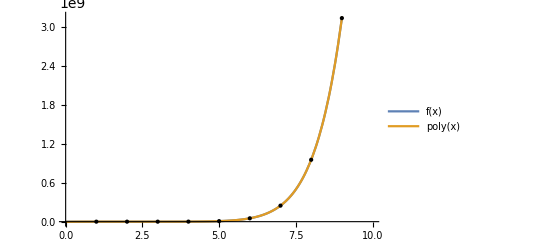

```mathematica
Plot[{f[x],poly[x]},{x,0,10},Epilog->{PointSize[Medium],Point[{xValues,fValues}//Transpose]},PlotLegends->"Expressions"]
```

```mathematica
{xValues3,fValues3}=Transpose@Table[{x,f[x]},{x,Range[3]}]
```

{{1,2,3},{1,683,44287}}

```mathematica
Vm=VandermondeMatrix[xValues3]
coefficients=LinearSolve[Vm,fValues3]
```

VandermondeMatrix[…]

{42241,-63701,21461}

```mathematica
poly[x_]:=coefficients.x^(Range[Length[coefficients]]-1)
```

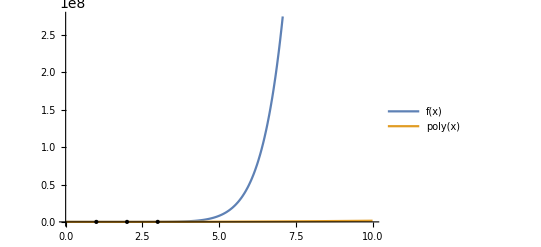

```mathematica
Plot[{f[x],poly[x]},{x,0,10},Epilog->{PointSize[Medium],Point[{xValues3,fValues3}//Transpose]},PlotLegends->"Expressions"]
```

```mathematica
poly/@Range[4]
```

{1,683,44287,130813}

```mathematica
f/@Range[4]
```

{1,683,44287,838861}

```mathematica
Transpose[{poly/@Range[4],f/@Range[4]}]
```

{{1,1},{683,683},{44287,44287},{130813,838861}}

```mathematica
Cases[{x_,y_}/;x!=y][Transpose[{poly/@Range[4],f/@Range[4]}]]
```

{{130813,838861}}

```mathematica
First[Cases[{x_,y_}/;x!=y][Transpose[{poly/@Range[4],f/@Range[4]}]]]
```

{130813,838861}

```mathematica
First[First[Cases[{x_,y_}/;x!=y][Transpose[{poly/@Range[4],f/@Range[4]}]]]]
```

130813

```mathematica
BOP//ClearAll
BOP[sequence_]:=First[First[Cases[{x_,y_}/;x!=y][sequence]]]
```

```mathematica
BOP[{{1,1},{683,683},{44287,44287},{130813,838861}}]
```

130813

```mathematica
poly//ClearAll
poly[x_]:=7x-6
f//ClearAll
f[x_]:=x^3
```

```mathematica
Transpose[{poly/@Range[3],f/@Range[3]}]
```

{{1,1},{8,8},{15,27}}

```mathematica
BOP[Transpose[{poly/@Range[3],f/@Range[3]}]]
```

15

```mathematica
InterpolatingPolynomial[{1,8},x]//Simplify
```

-6+7 x

```mathematica
InterpolatingPolynomial[{1,8,27},x]//Simplify
```

6-11 x+6 x^2

```mathematica
Table[Simplify@InterpolatingPolynomial[Table[b^3,{b,i}],x],{i,7}]
```

{1,-6+7 x,6-11 x+6 x^2,x^3,x^3,x^3,x^3}

```mathematica
Table[{Simplify@InterpolatingPolynomial[Table[b^3,{b,i}],x],Simplify@InterpolatingPolynomial[Table[b^3,{b,i}],x]/.{x->i+1}},{i,3}]
```

{{1,1},{-6+7 x,15},{6-11 x+6 x^2,58}}

```mathematica
Table[Simplify@InterpolatingPolynomial[Table[b^3,{b,i}],x]/.{x->i+1},{i,3}]
```

{1,15,58}

```mathematica
Total[Table[Simplify@InterpolatingPolynomial[Table[b^3,{b,i}],x]/.{x->i+1},{i,3}]]
```

74

```mathematica
Total[Table[Simplify@InterpolatingPolynomial[Table[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,{n,i}],x]/.{x->i+1},{i,10}]]
```

37076114526

```mathematica
Table[Simplify@InterpolatingPolynomial[Table[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,{n,i}],x],{i,7}]
```

{1,-681+682 x,1+11 (-1+x) (-3840+1951 x),1+11 (-1+x) (60528-51689 x+10728 x^2),1+11 (-1+x) (-398160+445223 x-161280 x^2+19112 x^3),1+11 (-1+x) (1337040-1781617 x+865380 x^2-183328 x^3+14460 x^4),1+11 (-1+x) (-2494800+3774551 x-2221380 x^2+641582 x^3-91980 x^4+5322 x^5)}

```mathematica
Remove@BOP
```

```mathematica
BOPSum//ClearAll
BOPSum[generatingPolynomial_,variable_,limit_]:=Total[Table[Simplify@InterpolatingPolynomial[Table[generatingPolynomial,{variable,i}],x]/.{x->i+1},{i,limit}]]
```

```mathematica
BOPSum[x^3,x,3]
```

74

```mathematica
BOPSum[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,n,10]
```

37076114526

```mathematica
Total[Table[InterpolatingPolynomial[Table[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,{n,i}],x]/.{x->i+1},{i,10}]]
```

37076114526

```mathematica
CoefficientRules[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,n]
```

{{10}→1,{9}→-1,{8}→1,{7}→-1,{6}→1,{5}→-1,{4}→1,{3}→-1,{2}→1,{1}→-1,{0}→1}

```mathematica
data=Association[CoefficientRules[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,n]]
```

<|{10}→1,{9}→-1,{8}→1,{7}→-1,{6}→1,{5}→-1,{4}→1,{3}→-1,{2}→1,{1}→-1,{0}→1|>

```mathematica
{Flatten@Keys[data],Values[data]}
```

{{10,9,8,7,6,5,4,3,2,1,0},{1,-1,1,-1,1,-1,1,-1,1,-1,1}}

```mathematica
Transpose[{Flatten@Keys[data],Values[data]}]
```

{{10,1},{9,-1},{8,1},{7,-1},{6,1},{5,-1},{4,1},{3,-1},{2,1},{1,-1},{0,1}}

```mathematica
Range[10,0,-1]
```

{10,9,8,7,6,5,4,3,2,1,0}

```mathematica
RandomInteger[{-20,20},11]
```

{6,17,-12,-9,19,-5,18,13,16,13,16}

```mathematica
Transpose[{Range[10,0,-1],RandomInteger[{-20,20},11]}]
```

{{10,16},{9,-4},{8,9},{7,-12},{6,15},{5,19},{4,-19},{3,-9},{2,-2},{1,-20},{0,-19}}

```mathematica
Rule@@@Transpose[{List/@Range[10,0,-1],RandomInteger[{-20,20},11]}]
```

{{10}→-11,{9}→15,{8}→-5,{7}→1,{6}→12,{5}→9,{4}→15,{3}→-4,{2}→18,{1}→-3,{0}→-11}

```mathematica
FromCoefficientRules[Rule@@@Transpose[{List/@Range[10,0,-1],RandomInteger[{-20,20},11]}],x]
```

19+13 x+17 x^2+x^3+4 x^4+11 x^5-4 x^6-4 x^7-19 x^8-2 x^9+8 x^10

```mathematica
Polynomial[coefficients_,exponents_]:=FromCoefficientRules[Rule@@@Transpose[{List/@exponents,coefficients}],x]
```

```mathematica
Polynomial[RandomInteger[{-20,20},101],Range[100,0,-1]]
```

x-7 x^2-15 x^3+15 x^4+20 x^5+16 x^6+16 x^7+7 x^8-4 x^9-20 x^10-5 x^11-16 x^12+18 x^13+3 x^14-7 x^15-10 x^16-16 x^17-10 x^18+4 x^19+x^20+14 x^21-19 x^22-9 x^23+5 x^24+15 x^25+3 x^26+11 x^27-15 x^28-11 x^29-10 x^30+4 x^31+20 x^32+6 x^33-20 x^34+9 x^35+2 x^36-20 x^37-6 x^38+15 x^39+16 x^40+16 x^41-20 x^42-12 x^43+9 x^44-20 x^45+20 x^46-16 x^47-20 x^48+2 x^49+x^50-2 x^51+2 x^52+10 x^53-15 x^54-10 x^55+9 x^56-10 x^57+12 x^58-3 x^59-18 x^60+20 x^61+2 x^62+3 x^63-15 x^64+14 x^65+9 x^66+17 x^67+14 x^68-20 x^70+8 x^71-x^72-5 x^73+9 x^74+15 x^75-20 x^76-x^77-10 x^78+4 x^79+5 x^80+17 x^81+15 x^82-12 x^83+9 x^84-5 x^86-12 x^87-14 x^88+x^89-18 x^90-15 x^91-7 x^92-9 x^93-19 x^94+12 x^95+12 x^96+3 x^97+15 x^98-19 x^99+2 x^100

```mathematica
RandomPolynomial[coefficentBounds_,exponent_]:=Polynomial[RandomInteger[coefficentBounds,exponent+1],Range[exponent,0,-1]]
```

```mathematica
RandomPolynomial[{-19,19},403]
```

-4-12 x+9 x^2+10 x^3+17 x^4+3 x^5+18 x^6-13 x^7+8 x^8+2 x^9+8 x^10-8 x^11-11 x^12-17 x^13+4 x^14-10 x^15-13 x^16-5 x^17+9 x^18-2 x^19-15 x^20+5 x^21+7 x^22-14 x^23+17 x^24-19 x^25-11 x^26+4 x^27-7 x^28+12 x^29+17 x^30-2 x^31+3 x^32+12 x^33-18 x^34+18 x^35+7 x^36+6 x^37-17 x^38+13 x^39-3 x^40+14 x^41+5 x^42-8 x^43+5 x^44+2 x^45-2 x^46-18 x^47-12 x^48+6 x^49+18 x^50-2 x^51+5 x^52-10 x^53-15 x^54+7 x^55+17 x^56+16 x^57-7 x^58+5 x^59+13 x^60+5 x^61-2 x^62-7 x^63-6 x^64+13 x^65+19 x^66-13 x^67-18 x^68+x^69+16 x^70-19 x^71+3 x^72+12 x^73-2 x^74+18 x^75-12 x^76-19 x^77+3 x^78-9 x^79-13 x^80-11 x^81-16 x^82+18 x^83+10 x^84-11 x^85-17 x^86+18 x^87-x^88+2 x^89+12 x^91-12 x^92-10 x^93-4 x^94+18 x^95-19 x^96+5 x^97-8 x^98+16 x^99+2 x^100+14 x^101+13 x^102+14 x^103-18 x^104-6 x^105+10 x^106-3 x^107-3 x^108-10 x^109+x^110-2 x^111+x^112+10 x^113-10 x^114-11 x^115+15 x^116+3 x^117-3 x^118+14 x^119-4 x^120+8 x^121+11 x^122+9 x^123+11 x^124+11 x^125-11 x^126+9 x^127+9 x^128-8 x^129+2 x^131+15 x^132+12 x^133-19 x^134+x^135-15 x^136+7 x^137-16 x^138+8 x^139+17 x^140+9 x^141-14 x^142-5 x^143-5 x^144+x^145+3 x^146+7 x^147+10 x^148-2 x^149+15 x^150-10 x^151-8 x^152+11 x^153+14 x^154-x^155+4 x^156+15 x^157-15 x^158+2 x^159-4 x^160-9 x^161+9 x^162-18 x^163+5 x^164-2 x^165+12 x^166-9 x^167+3 x^168+6 x^169+13 x^170-5 x^171+12 x^172-13 x^173-8 x^174-12 x^175+15 x^176-9 x^177-9 x^178-6 x^179+18 x^180+16 x^181-5 x^182+9 x^183-5 x^184-8 x^185+8 x^186+11 x^187+11 x^188-5 x^189+4 x^190+18 x^191+9 x^192+9 x^193+10 x^194-16 x^196-7 x^197-9 x^198-4 x^199-14 x^200-9 x^201-10 x^202+19 x^203-15 x^204-19 x^205+17 x^206-14 x^207-19 x^208-15 x^209-8 x^210+17 x^211+6 x^212+19 x^213-15 x^214-17 x^215+18 x^216-12 x^217+14 x^218-12 x^219-6 x^220+6 x^221+15 x^222+5 x^223-x^224-16 x^225-5 x^226-14 x^227-8 x^228+14 x^229-9 x^230+6 x^231-2 x^232-5 x^233-11 x^234+14 x^235+12 x^236+5 x^238+9 x^239+2 x^240-19 x^242-8 x^243-8 x^244+13 x^245-x^246+18 x^247-9 x^248+5 x^249-3 x^250-5 x^251-7 x^253-14 x^254+16 x^255-6 x^256+10 x^257-13 x^258-16 x^259+7 x^260+5 x^261+2 x^262-14 x^263+7 x^264+5 x^265+9 x^266+19 x^267+2 x^268+5 x^269-11 x^270-14 x^271-10 x^272-12 x^273+10 x^274+14 x^275-16 x^276+10 x^277-19 x^278+3 x^279+19 x^280+2 x^281-7 x^282+7 x^283-3 x^284+16 x^285-7 x^286+10 x^287+14 x^288+15 x^289+19 x^290-15 x^291-18 x^292+7 x^293+14 x^294-19 x^295+8 x^296-10 x^298-18 x^300+15 x^301+8 x^302-15 x^303+11 x^304-10 x^305+16 x^306-13 x^307+18 x^308+5 x^309+14 x^310+9 x^311+18 x^312+19 x^313-x^314+18 x^315+13 x^316-4 x^317-10 x^318-19 x^319-8 x^320+8 x^321+11 x^322+19 x^323-8 x^324-2 x^325+2 x^326+6 x^327+5 x^328-18 x^329+17 x^330+5 x^331+7 x^332-6 x^333-14 x^334-12 x^335+11 x^336-10 x^337-11 x^338+17 x^339+3 x^340-13 x^341+16 x^342-12 x^344+6 x^345-7 x^346-11 x^347-10 x^348+4 x^349-4 x^350+19 x^351+9 x^352+14 x^353-11 x^354+16 x^355+4 x^356+7 x^357-3 x^358+x^359-19 x^360-2 x^361+18 x^362+3 x^363+19 x^364+18 x^365-10 x^366+9 x^367-15 x^368-14 x^369+11 x^370-17 x^371+11 x^372+9 x^373-5 x^374-12 x^375-14 x^376+9 x^377-x^378+13 x^379+10 x^380-3 x^381-5 x^382-6 x^383-6 x^384-12 x^385-6 x^386+3 x^387+4 x^388+7 x^389-10 x^390-x^391-5 x^392+14 x^393-12 x^394+16 x^395+17 x^396-10 x^397+11 x^398+16 x^399-2 x^400-16 x^401-18 x^402-16 x^403

```mathematica
TeXForm[RandomPolynomial[{-19,19},14]]
```

```mathematica
SeedRandom[1]
RandomPolynomial[{-19,19},54]
```

RandomGeneratorState[…]

-1-11 x-15 x^2-14 x^3+13 x^4+2 x^5-13 x^6+7 x^7-2 x^8+3 x^9-15 x^10-4 x^11-8 x^12+5 x^13-x^14-x^15+4 x^16-17 x^17+15 x^18+6 x^19+11 x^20+2 x^21-3 x^22+x^23-16 x^24-2 x^25-5 x^26+2 x^27+x^28+10 x^29-19 x^30+10 x^32-4 x^33-18 x^34-7 x^35-5 x^36+2 x^37-8 x^38+6 x^39-17 x^40+5 x^41+11 x^42-7 x^43-2 x^44+14 x^45+12 x^46+14 x^47+9 x^48-3 x^49-16 x^50-13 x^51-17 x^52-18 x^53+x^54

```mathematica
SeedRandom[1]
BOPSum[RandomPolynomial[{-19,19},54],x,54]
```

RandomGeneratorState[…]

10003703588960973357462344453751809922032187195765909521404963905488114399624225450523175235308

```mathematica
SeedRandom[1]
TeXForm[-1-11 x-15 x^2-14 x^3+13 x^4+2 x^5-13 x^6+7 x^7-2 x^8+3 x^9-15 x^10-4 x^11-8 x^12+5 x^13-x^14-x^15+4 x^16-17 x^17+15 x^18+6 x^19+11 x^20+2 x^21-3 x^22+x^23-16 x^24-2 x^25-5 x^26+2 x^27+x^28+10 x^29-19 x^30+10 x^32-4 x^33-18 x^34-7 x^35-5 x^36+2 x^37-8 x^38+6 x^39-17 x^40+5 x^41+11 x^42-7 x^43-2 x^44+14 x^45+12 x^46+14 x^47+9 x^48-3 x^49-16 x^50-13 x^51-17 x^52-18 x^53+x^54]
```

RandomGeneratorState[…]

x^{54}-18 x^{53}-17 x^{52}-13 x^{51}-16 x^{50}-3 x^{49}+9 x^{48}+14 x^{47}+12 x^{46}+14 x^{45}-2 x^{44}-7 x^{43}+11 x^{42}+5 x^{41}-17 x^{40}+6
   x^{39}-8 x^{38}+2 x^{37}-5 x^{36}-7 x^{35}-18 x^{34}-4 x^{33}+10 x^{32}-19 x^{30}+10 x^{29}+x^{28}+2 x^{27}-5 x^{26}-2 x^{25}-16
   x^{24}+x^{23}-3 x^{22}+2 x^{21}+11 x^{20}+6 x^{19}+15 x^{18}-17 x^{17}+4 x^{16}-x^{15}-x^{14}+5 x^{13}-8 x^{12}-4 x^{11}-15 x^{10}+3 x^9-2
   x^8+7 x^7-13 x^6+2 x^5+13 x^4-14 x^3-15 x^2-11 x-1

```mathematica
BOPSum[-1-11 x-15 x^2-14 x^3+13 x^4+2 x^5-13 x^6+7 x^7-2 x^8+3 x^9-15 x^10-4 x^11-8 x^12+5 x^13-x^14-x^15+4 x^16-17 x^17+15 x^18+6 x^19+11 x^20+2 x^21-3 x^22+x^23-16 x^24-2 x^25-5 x^26+2 x^27+x^28+10 x^29-19 x^30+10 x^32-4 x^33-18 x^34-7 x^35-5 x^36+2 x^37-8 x^38+6 x^39-17 x^40+5 x^41+11 x^42-7 x^43-2 x^44+14 x^45+12 x^46+14 x^47+9 x^48-3 x^49-16 x^50-13 x^51-17 x^52-18 x^53+x^54,x,54]
```

10003703588960973357462344453751809922032187195765909521404963905488114399624225450523175235308

```mathematica
SeedRandom[1]
BlockRandom[randomPolynomial=RandomPolynomial[{-19,19},148]]
BOPSum[randomPolynomial,x,148]
```

RandomGeneratorState[…]

19-15 x-13 x^2+8 x^3+19 x^4+18 x^5+5 x^6-9 x^7+5 x^8-14 x^9-4 x^10-9 x^11-6 x^12+18 x^13+18 x^14-9 x^15+2 x^16-2 x^17+19 x^18+7 x^19+5 x^20+11 x^21-8 x^22+2 x^23-15 x^24+8 x^25-13 x^26+6 x^27-8 x^28-4 x^29+4 x^30+6 x^31+13 x^32+9 x^33-5 x^34+6 x^35-14 x^36-16 x^37+19 x^38-4 x^39-11 x^40-9 x^41-x^42-14 x^43+9 x^44+6 x^45-x^46-10 x^47-17 x^48+4 x^49-11 x^50+3 x^51-3 x^52-7 x^53-16 x^54+17 x^55+5 x^56-17 x^57+19 x^58-x^59+2 x^60-2 x^61-2 x^62-5 x^63+12 x^64-4 x^65-5 x^66+4 x^67+18 x^68+13 x^69+2 x^70-19 x^71+10 x^72+8 x^73+12 x^74+19 x^75+10 x^76+18 x^77-14 x^78+3 x^79-12 x^80+13 x^81-16 x^82+8 x^83-x^84-18 x^85+18 x^86+4 x^87+16 x^88+11 x^89+16 x^90-5 x^91+13 x^92+3 x^93-x^94-11 x^95-15 x^96-14 x^97+13 x^98+2 x^99-13 x^100+7 x^101-2 x^102+3 x^103-15 x^104-4 x^105-8 x^106+5 x^107-x^108-x^109+4 x^110-17 x^111+15 x^112+6 x^113+11 x^114+2 x^115-3 x^116+x^117-16 x^118-2 x^119-5 x^120+2 x^121+x^122+10 x^123-19 x^124+10 x^126-4 x^127-18 x^128-7 x^129-5 x^130+2 x^131-8 x^132+6 x^133-17 x^134+5 x^135+11 x^136-7 x^137-2 x^138+14 x^139+12 x^140+14 x^141+9 x^142-3 x^143-16 x^144-13 x^145-17 x^146-18 x^147+x^148

5944223068486913689803243513913060543365059308033731860035337597148084268267310091804761578531300559540111277284371351324600233812981947139665247842802889376601160563109861505245500695047695263273568969484195208119467342846335787074236372091405976660168368430015881508383675342509684415750346441289028298744173191076299789

```mathematica
Table[Expand@InterpolatingPolynomial[Table[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,{n,i}],x],{i,7}]
```

{1,-681+682 x,42241-63701 x+21461 x^2,-665807+1234387 x-686587 x^2+118008 x^3,4379761-9277213 x+6671533 x^2-1984312 x^3+210232 x^4,-14707439+34305227 x-29116967 x^2+11535788 x^3-2175668 x^4+159060 x^5,27442801-68962861 x+65955241 x^2-31492582 x^3+8069182 x^4-1070322 x^5+58542 x^6}

```mathematica
f3[x_]:=42241-63701 x+21461 x^2
{x3Values,f3Values}=Transpose@Table[{x,f3[x]},{x,Range[3]}]
```

{{1,2,3},{1,683,44287}}

```mathematica
g//ClearAll
g[n_]:=1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10
```

```mathematica
g[Range[4]]
```

{1,683,44287,838861}

```mathematica
Vm3=VandermondeMatrix[x3Values];
coefficients3=LinearSolve[Vm3,f3Values];
```

```mathematica
poly3[x_]=coefficients3.x^(Range[Length[coefficients3]]-1)
```

42241-63701 x+21461 x^2

```mathematica
Table[Expand@InterpolatingPolynomial[Table[1-n+n^2-n^3+n^4-n^5+n^6-n^7+n^8-n^9+n^10,{n,i}],x],{i,7}]
```

```mathematica
randomPoly
```

```mathematica
TeXForm[19-15 x-13 x^2+8 x^3+19 x^4+18 x^5+5 x^6-9 x^7+5 x^8-14 x^9-4 x^10-9 x^11-6 x^12+18 x^13+18 x^14-9 x^15+2 x^16-2 x^17+19 x^18+7 x^19+5 x^20+11 x^21-8 x^22+2 x^23-15 x^24+8 x^25-13 x^26+6 x^27-8 x^28-4 x^29+4 x^30+6 x^31+13 x^32+9 x^33-5 x^34+6 x^35-14 x^36-16 x^37+19 x^38-4 x^39-11 x^40-9 x^41-x^42-14 x^43+9 x^44+6 x^45-x^46-10 x^47-17 x^48+4 x^49-11 x^50+3 x^51-3 x^52-7 x^53-16 x^54+17 x^55+5 x^56-17 x^57+19 x^58-x^59+2 x^60-2 x^61-2 x^62-5 x^63+12 x^64-4 x^65-5 x^66+4 x^67+18 x^68+13 x^69+2 x^70-19 x^71+10 x^72+8 x^73+12 x^74+19 x^75+10 x^76+18 x^77-14 x^78+3 x^79-12 x^80+13 x^81-16 x^82+8 x^83-x^84-18 x^85+18 x^86+4 x^87+16 x^88+11 x^89+16 x^90-5 x^91+13 x^92+3 x^93-x^94-11 x^95-15 x^96-14 x^97+13 x^98+2 x^99-13 x^100+7 x^101-2 x^102+3 x^103-15 x^104-4 x^105-8 x^106+5 x^107-x^108-x^109+4 x^110-17 x^111+15 x^112+6 x^113+11 x^114+2 x^115-3 x^116+x^117-16 x^118-2 x^119-5 x^120+2 x^121+x^122+10 x^123-19 x^124+10 x^126-4 x^127-18 x^128-7 x^129-5 x^130+2 x^131-8 x^132+6 x^133-17 x^134+5 x^135+11 x^136-7 x^137-2 x^138+14 x^139+12 x^140+14 x^141+9 x^142-3 x^143-16 x^144-13 x^145-17 x^146-18 x^147+x^148]
```

x^{148}-18 x^{147}-17 x^{146}-13 x^{145}-16 x^{144}-3 x^{143}+9 x^{142}+14 x^{141}+12 x^{140}+14 x^{139}-2 x^{138}-7 x^{137}+11 x^{136}+5
   x^{135}-17 x^{134}+6 x^{133}-8 x^{132}+2 x^{131}-5 x^{130}-7 x^{129}-18 x^{128}-4 x^{127}+10 x^{126}-19 x^{124}+10 x^{123}+x^{122}+2 x^{121}-5
   x^{120}-2 x^{119}-16 x^{118}+x^{117}-3 x^{116}+2 x^{115}+11 x^{114}+6 x^{113}+15 x^{112}-17 x^{111}+4 x^{110}-x^{109}-x^{108}+5 x^{107}-8
   x^{106}-4 x^{105}-15 x^{104}+3 x^{103}-2 x^{102}+7 x^{101}-13 x^{100}+2 x^{99}+13 x^{98}-14 x^{97}-15 x^{96}-11 x^{95}-x^{94}+3 x^{93}+13
   x^{92}-5 x^{91}+16 x^{90}+11 x^{89}+16 x^{88}+4 x^{87}+18 x^{86}-18 x^{85}-x^{84}+8 x^{83}-16 x^{82}+13 x^{81}-12 x^{80}+3 x^{79}-14 x^{78}+18
   x^{77}+10 x^{76}+19 x^{75}+12 x^{74}+8 x^{73}+10 x^{72}-19 x^{71}+2 x^{70}+13 x^{69}+18 x^{68}+4 x^{67}-5 x^{66}-4 x^{65}+12 x^{64}-5 x^{63}-2
   x^{62}-2 x^{61}+2 x^{60}-x^{59}+19 x^{58}-17 x^{57}+5 x^{56}+17 x^{55}-16 x^{54}-7 x^{53}-3 x^{52}+3 x^{51}-11 x^{50}+4 x^{49}-17 x^{48}-10
   x^{47}-x^{46}+6 x^{45}+9 x^{44}-14 x^{43}-x^{42}-9 x^{41}-11 x^{40}-4 x^{39}+19 x^{38}-16 x^{37}-14 x^{36}+6 x^{35}-5 x^{34}+9 x^{33}+13
   x^{32}+6 x^{31}+4 x^{30}-4 x^{29}-8 x^{28}+6 x^{27}-13 x^{26}+8 x^{25}-15 x^{24}+2 x^{23}-8 x^{22}+11 x^{21}+5 x^{20}+7 x^{19}+19 x^{18}-2
   x^{17}+2 x^{16}-9 x^{15}+18 x^{14}+18 x^{13}-6 x^{12}-9 x^{11}-4 x^{10}-14 x^9+5 x^8-9 x^7+5 x^6+18 x^5+19 x^4+8 x^3-13 x^2-15 x+19

```mathematica
CopyToClipboard[TeXForm[19-15 x-13 x^2+8 x^3+19 x^4+18 x^5+5 x^6-9 x^7+5 x^8-14 x^9-4 x^10-9 x^11-6 x^12+18 x^13+18 x^14-9 x^15+2 x^16-2 x^17+19 x^18+7 x^19+5 x^20+11 x^21-8 x^22+2 x^23-15 x^24+8 x^25-13 x^26+6 x^27-8 x^28-4 x^29+4 x^30+6 x^31+13 x^32+9 x^33-5 x^34+6 x^35-14 x^36-16 x^37+19 x^38-4 x^39-11 x^40-9 x^41-x^42-14 x^43+9 x^44+6 x^45-x^46-10 x^47-17 x^48+4 x^49-11 x^50+3 x^51-3 x^52-7 x^53-16 x^54+17 x^55+5 x^56-17 x^57+19 x^58-x^59+2 x^60-2 x^61-2 x^62-5 x^63+12 x^64-4 x^65-5 x^66+4 x^67+18 x^68+13 x^69+2 x^70-19 x^71+10 x^72+8 x^73+12 x^74+19 x^75+10 x^76+18 x^77-14 x^78+3 x^79-12 x^80+13 x^81-16 x^82+8 x^83-x^84-18 x^85+18 x^86+4 x^87+16 x^88+11 x^89+16 x^90-5 x^91+13 x^92+3 x^93-x^94-11 x^95-15 x^96-14 x^97+13 x^98+2 x^99-13 x^100+7 x^101-2 x^102+3 x^103-15 x^104-4 x^105-8 x^106+5 x^107-x^108-x^109+4 x^110-17 x^111+15 x^112+6 x^113+11 x^114+2 x^115-3 x^116+x^117-16 x^118-2 x^119-5 x^120+2 x^121+x^122+10 x^123-19 x^124+10 x^126-4 x^127-18 x^128-7 x^129-5 x^130+2 x^131-8 x^132+6 x^133-17 x^134+5 x^135+11 x^136-7 x^137-2 x^138+14 x^139+12 x^140+14 x^141+9 x^142-3 x^143-16 x^144-13 x^145-17 x^146-18 x^147+x^148]]
```